# Trave continua

```mathematica
ClearAll["Global`*"];

v1[s1_] = c1+c2*s1+c3*Cos[α*s1]+c4*Sin[α*s1];
v2[s2_] = c5+c6*s2+c7*Cos[α*s2]+c8*Sin[α*s2];

{RR, MM} = CoefficientArrays[
{
v1[0]==0,
v1''[0]==0,
v1[l]==0,
v2[0]==0,
v1'[l]==v2'[0],
v1''[l]==v2''[0],
v2[l]==0,
v2''[l]==0
},
{c1, c2, c3, c4, c5, c6, c7, c8}
]//Normal;
RR = -RR;
MatrixForm[MM]
MatrixForm[RR]
```

(1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | -α^2 | 0 | 0 | 0 | 0 | 0
1 | l | Cos[l α] | Sin[l α] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 1 | -α Sin[l α] | α Cos[l α] | 0 | -1 | 0 | -α
0 | 0 | -α^2 Cos[l α] | -α^2 Sin[l α] | 0 | 0 | α^2 | 0
0 | 0 | 0 | 0 | 1 | l | Cos[l α] | Sin[l α]
0 | 0 | 0 | 0 | 0 | 0 | -α^2 Cos[l α] | -α^2 Sin[l α])

(0
0
0
0
0
0
0
0)

```mathematica
detMM[α_]=Det[MM]//Simplify
```

-2 l α^6 (l α Cos[l α]-Sin[l α]) Sin[l α]

## Primo modo critico

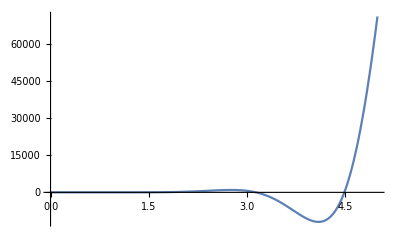

```mathematica
Plot[detMM[α], {α, 0, 5}, PlotRange->Full]
```

```mathematica
α/.FindRoot[detMM[α]==0, {α, 3}]
```

3.14159

```mathematica
ClearAll[αcr, l,k]
l=1;
αcr = Simplify[k*Pi/l];

MMcr = Simplify[MM/.α->αcr, Assumptions->k ∈ Integers]//Chop;
MatrixForm[MMcr]
```

(1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | -k^2 π^2 | 0 | 0 | 0 | 0 | 0
1 | 1 | (-1)^k | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 1 | 0 | (-1)^k k π | 0 | -1 | 0 | -k π
0 | 0 | (-1)^(1+k) k^2 π^2 | 0 | 0 | 0 | k^2 π^2 | 0
0 | 0 | 0 | 0 | 1 | 1 | (-1)^k | 0
0 | 0 | 0 | 0 | 0 | 0 | (-1)^(1+k) k^2 π^2 | 0)

```mathematica
{c1, c2, c3, c4, c5, c6, c7, c8} = Eigenvectors[MMcr][[1]]//Chop
```

{0,0,0,(-1)^(2-k),0,0,0,1}

```mathematica
v1[s1]
v2[s2]
```

(-1)^(2-k) Sin[s1 α]

Sin[s2 α]

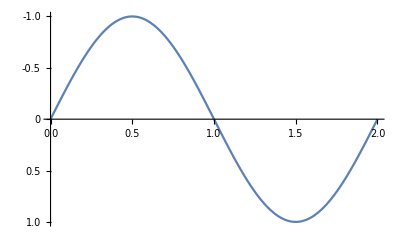

```mathematica
k=1;
Show[
Plot[v1[s]/.α->αcr, {s, 0, l}, ScalingFunctions->"Reverse"],
Plot[v2[s-l]/.α->αcr, {s, l, 2l}, ScalingFunctions->"Reverse"],
PlotRange->Full
]
```

## Primo carico critico

```mathematica
EJ=1;
Pcr = αcr^2*EJ//N
```

π^2

## Secondo modo critico

```mathematica
Plot[detMM[α], {α, 0, 5}, PlotRange->Full]
```

-Graphics-

```mathematica
ClearAll[αcr, l]
l=1;
αcr = α/.FindRoot[detMM[α]==0, {α, 5}]
```

4.49341

```mathematica
MMcr = Simplify[MM/.α->αcr]//Chop;
MatrixForm[MMcr]
```

(1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | -20.1907 | 0 | 0 | 0 | 0 | 0
1 | 1 | -0.217234 | -0.97612 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 1 | 4.38611 | -0.97612 | 0 | -1 | 0 | -4.49341
0 | 0 | 4.38611 | 19.7086 | 0 | 0 | 20.1907 | 0
0 | 0 | 0 | 0 | 1 | 1 | -0.217234 | -0.97612
0 | 0 | 0 | 0 | 0 | 0 | 4.38611 | 19.7086)

```mathematica
{c1, c2, c3, c4, c5, c6, c7, c8} = Eigenvectors[MMcr]//Last//Chop
```

{0,-0.442848,0,-0.453683,-0.442848,0.442848,0.442848,-0.0985551}

```mathematica
v1[s1]
v2[s2]
```

-0.442848 s1-0.453683 Sin[s1 α]

-0.442848+0.442848 s2+0.442848 Cos[s2 α]-0.0985551 Sin[s2 α]

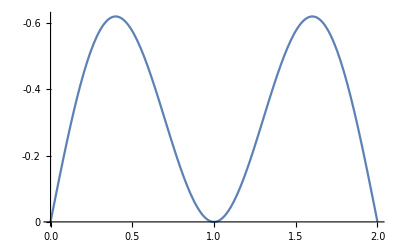

```mathematica
Show[
Plot[v1[s]/.α->αcr, {s, 0, l}, ScalingFunctions->"Reverse"],
Plot[v2[s-l]/.α->αcr, {s, l, 2l}, ScalingFunctions->"Reverse"],
PlotRange->Full
]
```

## Secondo carico critico

```mathematica
EJ=1;
Pcr = αcr^2*EJ
```

20.1907

## Terzo modo critico

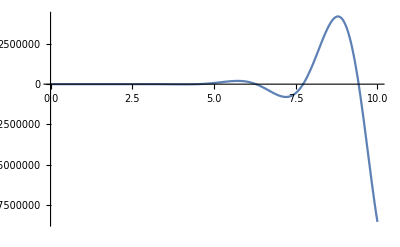

```mathematica
Plot[detMM[α], {α, 0, 10}, PlotRange->Full]
```

```mathematica
α/.FindRoot[detMM[α]==0, {α, 6}]
```

6.28319

```mathematica
ClearAll[αcr, l, k]
l=1;
αcr = Simplify[k*Pi/l];

MMcr = Simplify[MM/.α->αcr, Assumptions->k ∈ Integers]//Chop;
MatrixForm[MMcr]
```

(1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | -k^2 π^2 | 0 | 0 | 0 | 0 | 0
1 | 1 | (-1)^k | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 1 | 0 | (-1)^k k π | 0 | -1 | 0 | -k π
0 | 0 | (-1)^(1+k) k^2 π^2 | 0 | 0 | 0 | k^2 π^2 | 0
0 | 0 | 0 | 0 | 1 | 1 | (-1)^k | 0
0 | 0 | 0 | 0 | 0 | 0 | (-1)^(1+k) k^2 π^2 | 0)

```mathematica
{c1, c2, c3, c4, c5, c6, c7, c8} = Eigenvectors[MMcr][[1]]//Chop
```

{0,0,0,(-1)^(2-k),0,0,0,1}

```mathematica
v1[s1]
v2[s2]
```

(-1)^(2-k) Sin[s1 α]

Sin[s2 α]

6.28319

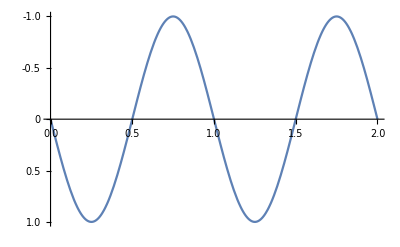

```mathematica
k=2;
αcr//N
Show[
Plot[v1[s]/.α->αcr, {s, 0, l}, ScalingFunctions->"Reverse"],
Plot[v2[s-l]/.α->αcr, {s, l, 2l}, ScalingFunctions->"Reverse"],
PlotRange->Full
]
```

## Terzo carico critico

```mathematica
EJ=1;
Pcr = αcr^2*EJ//N
```

39.4784

## Quarto modo critico

```mathematica
Plot[detMM[α], {α, 0, 10}, PlotRange->Full]
```

-Graphics-

```mathematica
ClearAll[αcr, l]
l=1;
αcr = α/.FindRoot[detMM[α]==0, {α, 8}]
```

7.72525

```mathematica
MMcr = Simplify[MM/.α->αcr]//Chop;
MatrixForm[MMcr]
```

(1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | -59.6795 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0.128375 | 0.991726 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 1 | -7.66133 | 0.991726 | 0 | -1 | 0 | -7.72525
0 | 0 | -7.66133 | -59.1857 | 0 | 0 | 59.6795 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0.128375 | 0.991726
0 | 0 | 0 | 0 | 0 | 0 | -7.66133 | -59.1857)

```mathematica
{c1, c2, c3, c4, c5, c6, c7, c8} = Eigenvectors[MMcr]//Last//Chop
```

{0,-0.445722,0,0.449441,-0.445722,0.445722,0.445722,-0.0576968}

```mathematica
v1[s1]
v2[s2]
```

-0.445722 s1+0.449441 Sin[s1 α]

-0.445722+0.445722 s2+0.445722 Cos[s2 α]-0.0576968 Sin[s2 α]

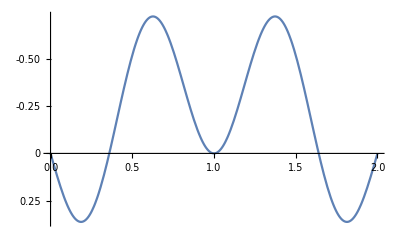

```mathematica
Show[
Plot[v1[s]/.α->αcr, {s, 0, l}, ScalingFunctions->"Reverse"],
Plot[v2[s-l]/.α->αcr, {s, l, 2l}, ScalingFunctions->"Reverse"],
PlotRange->Full
]
```

## Quarto carico critico

```mathematica
EJ=1;
Pcr = αcr^2*EJ//N
```

59.6795

## Quinto modo critico

```mathematica
Plot[detMM[α], {α, 0, 10}, PlotRange->Full]
```

-Graphics-

```mathematica
α/.FindRoot[detMM[α]==0, {α, 9}]
```

9.42478

```mathematica
ClearAll[αcr, l, k]
l=1;
αcr = Simplify[k*Pi/l];

MMcr = Simplify[MM/.α->αcr, Assumptions->k ∈ Integers]//Chop;
MatrixForm[MMcr]
```

(1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | -k^2 π^2 | 0 | 0 | 0 | 0 | 0
1 | 1 | (-1)^k | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 1 | 0 | (-1)^k k π | 0 | -1 | 0 | -k π
0 | 0 | (-1)^(1+k) k^2 π^2 | 0 | 0 | 0 | k^2 π^2 | 0
0 | 0 | 0 | 0 | 1 | 1 | (-1)^k | 0
0 | 0 | 0 | 0 | 0 | 0 | (-1)^(1+k) k^2 π^2 | 0)

```mathematica
{c1, c2, c3, c4, c5, c6, c7, c8} = Eigenvectors[MMcr][[1]]//Chop
```

{0,0,0,(-1)^(2-k),0,0,0,1}

```mathematica
v1[s1]
v2[s2]
```

(-1)^(2-k) Sin[s1 α]

Sin[s2 α]

9.42478

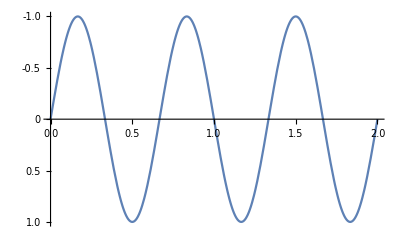

```mathematica
k=3;
αcr//N
Show[
Plot[v1[s]/.α->αcr, {s, 0, l}, ScalingFunctions->"Reverse"],
Plot[v2[s-l]/.α->αcr, {s, l, 2l}, ScalingFunctions->"Reverse"],
PlotRange->Full
]
```

## Quinto carico critico

```mathematica
EJ=1;
Pcr = αcr^2*EJ//N
```

88.8264

## Sesto modo critico

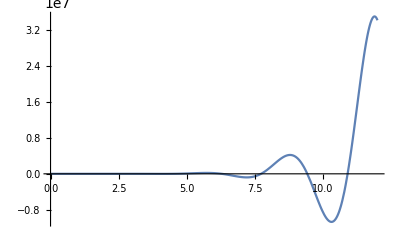

```mathematica
Plot[detMM[α], {α, 0, 12}, PlotRange->Full]
```

```mathematica
ClearAll[αcr, l]
l=1;
αcr = α/.FindRoot[detMM[α]==0, {α, 11}]
```

10.9041

```mathematica
MMcr = Simplify[MM/.α->αcr]//Chop;
MatrixForm[MMcr]
```

(1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | -118.9 | 0 | 0 | 0 | 0 | 0
1 | 1 | -0.0913252 | -0.995821 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 1 | 10.8586 | -0.995821 | 0 | -1 | 0 | -10.9041
0 | 0 | 10.8586 | 118.403 | 0 | 0 | 118.9 | 0
0 | 0 | 0 | 0 | 1 | 1 | -0.0913252 | -0.995821
0 | 0 | 0 | 0 | 0 | 0 | 10.8586 | 118.403)

```mathematica
{c1, c2, c3, c4, c5, c6, c7, c8} = Eigenvectors[MMcr]//Last//Chop
```

{0,0.446463,0,0.448337,0.446463,-0.446463,-0.446463,0.0409444}

```mathematica
v1[s1]
v2[s2]
```

0.446463 s1+0.448337 Sin[s1 α]

0.446463-0.446463 s2-0.446463 Cos[s2 α]+0.0409444 Sin[s2 α]

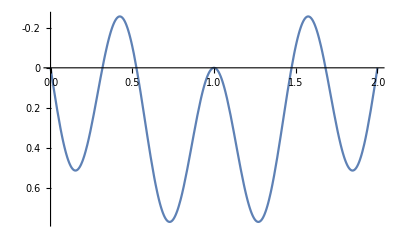

```mathematica
Show[
Plot[v1[s]/.α->αcr, {s, 0, l}, ScalingFunctions->"Reverse"],
Plot[v2[s-l]/.α->αcr, {s, l, 2l}, ScalingFunctions->"Reverse"],
PlotRange->Full
]
```

## Sesto carico critico

```mathematica
EJ=1;
Pcr = αcr^2*EJ//N
```

118.9

# Trave continua su appoggio elastico

```mathematica
ClearAll["Global`*"];

v1[s1_] = c1+c2*s1+c3*Cos[α*s1]+c4*Sin[α*s1];
v2[s2_] = c5+c6*s2+c7*Cos[α*s2]+c8*Sin[α*s2];

{RR, MM} = CoefficientArrays[
{
v1[0]==0,
v1''[0]==0,
v1[l/2]==v2[0],
v1'[l/2]==v2'[0],
v1''[l/2]==v2''[0],
-(v1'''[l/2]+α^2*v1'[l/2])+(v2'''[0]+α^2*v2'[0])+β*π^2/l^3*v1[l/2],
v2[l/2]==0,
v2''[l/2]==0
},
{c1, c2, c3, c4, c5, c6, c7, c8}
]//Normal;
RR = -RR;
MatrixForm[MM]
MatrixForm[RR]
```

(1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | -α^2 | 0 | 0 | 0 | 0 | 0
1 | l/2 | Cos[(l α)/2] | Sin[(l α)/2] | -1 | 0 | -1 | 0
0 | 1 | -α Sin[(l α)/2] | α Cos[(l α)/2] | 0 | -1 | 0 | -α
0 | 0 | -α^2 Cos[(l α)/2] | -α^2 Sin[(l α)/2] | 0 | 0 | α^2 | 0
(π^2 β)/l^3 | -α^2+(π^2 β)/(2 l^2) | (π^2 β Cos[(l α)/2])/l^3 | (π^2 β Sin[(l α)/2])/l^3 | 0 | α^2 | 0 | 0
0 | 0 | 0 | 0 | 1 | l/2 | Cos[(l α)/2] | Sin[(l α)/2]
0 | 0 | 0 | 0 | 0 | 0 | -α^2 Cos[(l α)/2] | -α^2 Sin[(l α)/2])

(0
0
0
0
0
0
0
0)

```mathematica
detMM[α_]=Det[MM]//Simplify
```

(α^6 (4 π^2 β Sin[(l α)/2]^2+l α (4 l^2 α^2-π^2 β) Sin[l α]))/(4 l^2)

```mathematica
Sin[2*u]^2+u*Sin[4*u]*(64*u^2/(π^2*β)-1)//TrigExpand//FullSimplify
```

Sin[2 u] (2 u (-1+(64 u^2)/(π^2 β)) Cos[2 u]+Sin[2 u])

```mathematica
Sin[2u]^2-u*Sin[4u]//TrigExpand//FullSimplify
```

Sin[2 u] (-2 u Cos[2 u]+Sin[2 u])

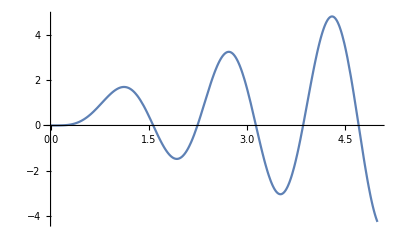

```mathematica
Plot[Sin[2u]^2-u*Sin[4u], {u, 0, 5}]
```

```mathematica
Limit[detMM[α], β->0]
```

l α^9 Sin[l α]

```mathematica
detMM[α]//TrigExpand//FullSimplify
```

(α^6 (-2 π^2 β (-1+Cos[l α])+l α (4 l^2 α^2-π^2 β) Sin[l α]))/(4 l^2)